```mathematica
empiricalDistribution=EmpiricalDistribution[{2/3,1/3}->{1,2}]
```

```mathematica
F
```

```mathematica
Integrate[x^2, {x, 0, 1}]
```

1/3

```mathematica
Integrate[k, {x, 1, 4/3}]
```

k/3

```mathematica
Integrate[2 - (3/2)x, {x, 0, 1}]
```

5/4

```mathematica
Integrate[x^2, {x, 0, 1}] + Integrate[k, {x, 1, 4/3}] + Integrate[2 - (3/2)x, {x, 0, 1}]
```

19/12+k/3

```mathematica
Solve[Integrate[x^2, {x, 0, 1}] + Integrate[k, {x, 1, 4/3}] + Integrate[2 - (3/2)x, {x, 0, 1}] == 1, k]
```

{{k→-7/4}}

```mathematica
4/3 - 1
```

1/3

```mathematica
Integrate[3 - (3/2)x, {x, 4/3, 2}]
```

1/3

```mathematica
Solve[Integrate[x^2, {x, 0, 1}] + Integrate[k, {x, 1, 4/3}] + Integrate[3 - (3/2)x, {x, 4/3, 2}], k]
```

Solve::naqs: 2/3 + k/3 is not a quantified system of equations and inequalities.

Solve[2/3+k/3,k]

```mathematica
Solve[Integrate[x^2, {x, 0, 1}] + Integrate[k, {x, 1, 4/3}] + Integrate[3 - (3/2)x, {x, 4/3, 2} == 1, k]
```

```mathematica
Solve[Integrate[x^2, {x, 0, 1}] + Integrate[k, {x, 1, 4/3}] + Integrate[3 - (3/2)x, {x, 4/3, 2}] == 1, k]
```

{{k→1}}

```mathematica
Integrate[x^2, {x, 0, 1}]
```

1/3

```mathematica
Integrate[k, {x, 1, 4/3}]
```

k/3

```mathematica
Integrate[3 - (3/2)x, {x, 4/3, 2}]
```

1/3

```mathematica
Integrate[x^2, {x, 0, 1}] + Integrate[k, {x, 1, 4/3}] + Integrate[3 - (3/2)x, {x, 4/3, 2}]
```

2/3+k/3

```mathematica
Integrate[x * x^2, {x, 0, 1}] + Integrate[x * k, {x, 1, 4/3}] + Integrate[(3 - (3/2)x) * x, {x, 4/3, 2}]
```

83/108+(7 k)/18

```mathematica
Integrate[x * x^2, {x, 0, 1}] + Integrate[x * 1, {x, 1, 4/3}] + Integrate[(3 - (3/2)x) * x, {x, 4/3, 2}]
```

125/108

```mathematica
125/108
```

125/108

```mathematica
N[125/108]
```

1.15741

```mathematica
Integrate[x^2 * x^2, {x, 0, 1}] + Integrate[x^2 * 1, {x, 1, 4/3}] + Integrate[(3 - (3/2)x) * x^2, {x, 4/3, 2}]
```

596/405

```mathematica
N[596/405]
```

1.4716

```mathematica
1.4716-(1.15741)^2
```

0.132002

```mathematica
Sqrt[0.1320020919]
```

0.363321

```mathematica
N[4/3]
```

1.33333

```mathematica
Integrate[3 - (3/2)x, {x, 1.25, 1.75}]
```

0.375

```mathematica
Plot[Piecewise[{{(x^3) / 3,0 < x && x<1},{x, 1 < x && x < 4/3}, {(-3(x^2)/ 2) + 3*x, 4/3 < x && x < 2},  {1, 2 < x},{x,-1,1}]
```

```mathematica
Plot[Piecewise[{{(x^3) / 3,0 < x && x<1},{x, 1 < x && x < 4/3}, {(-3(x^2)/ 2) + 3*x, 4/3 < x && x < 2},  {1, 2 < x},{x,-1,1}]]
```

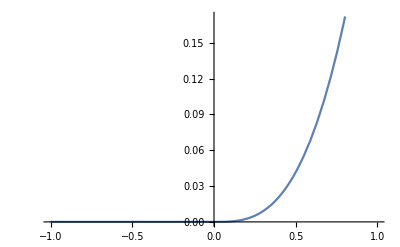

```mathematica
Plot[Piecewise[{{(x^3) / 3,0 < x && x<1},{x, 1 < x && x < 4/3}, {(-3(x^2)/ 2) + 3*x, 4/3 < x && x < 2},  {1, 2 < x}}],{x,-1,1}]
```

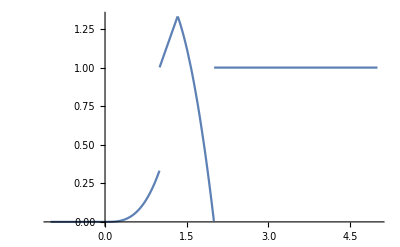

```mathematica
Plot[Piecewise[{{(x^3) / 3,0 < x && x<1},{x, 1 < x && x < 4/3}, {(-3(x^2)/ 2) + 3*x, 4/3 < x && x < 2},  {1, 2 < x}}],{x,-1,5}]
```

```mathematica
Factorial[8]
```

40320

```mathematica
120/40320
```

1/336

```mathematica
N[1/336]
```

0.00297619

```mathematica
240/40320
```

1/168

```mathematica
N[1/168]
```

0.00595238

```mathematica
{DiscretePlot[PDF[𝒟,x],{x,data}],DiscretePlot[CDF[𝒟,x],{x,-4,4,.01}]}
```

```mathematica
CDF[empiricalDistribution,x]
```

2/3 Boole[1≤x]+1/3 Boole[2≤x]

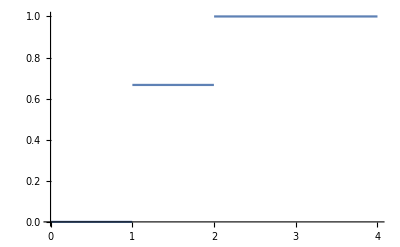

```mathematica
Plot[CDF[empiricalDistribution][x],{x,0,4}]
```

```mathematica
Plot[empiricalDistribution[x],{x,0,4}]
```

-Graphics-

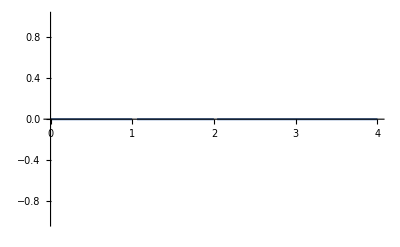

```mathematica
Plot[PDF[empiricalDistribution][x],{x,0,4}]
```

```mathematica
𝒟=EmpiricalDistribution[data];
```

EmpiricalDistribution::rectn: Rectangular array of real numbers is expected at position 1 in EmpiricalDistribution[data].

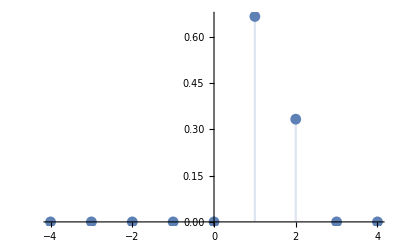
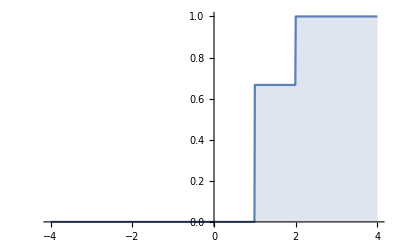

```mathematica
{DiscretePlot[PDF[empiricalDistribution,x],{x, -4, 4}],DiscretePlot[CDF[empiricalDistribution,x],{x,-4,4,.01}]}
```

```mathematica
DiscretePlot[PDF[empiricalDistribution,x],{x, -4, 4}]
```

-Graphics-

```mathematica
empiricalDistribution=EmpiricalDistribution[{0.69,0.185, 0.0925, 0.0185, 0.0092}->{-10,0, 10, 40, 70}]
```

DataDistribution[…]

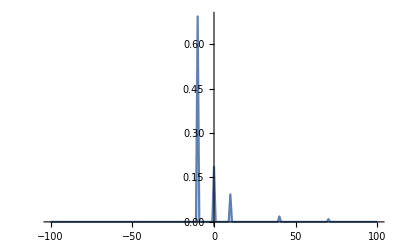

```mathematica
DiscretePlot[PDF[empiricalDistribution,x],{x, -100, 100}]
```

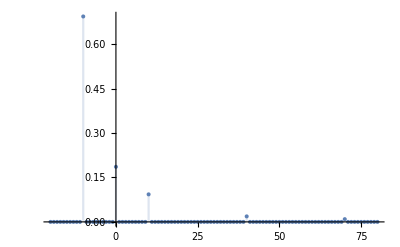

```mathematica
DiscretePlot[PDF[empiricalDistribution,x],{x, -20, 80}]
```

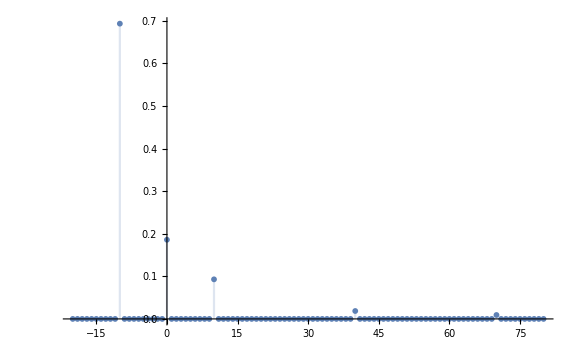

```mathematica
Show[%11,ImageSize->Large]
```

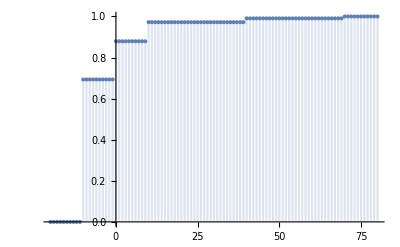

```mathematica
DiscretePlot[CDF[empiricalDistribution,x],{x, -20, 80}]
```

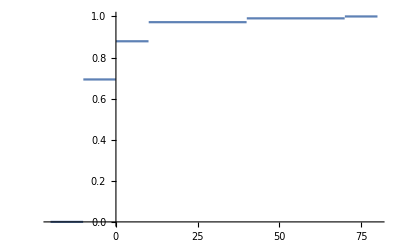

```mathematica
Plot[CDF[empiricalDistribution][x],{x,-20,80}]
```

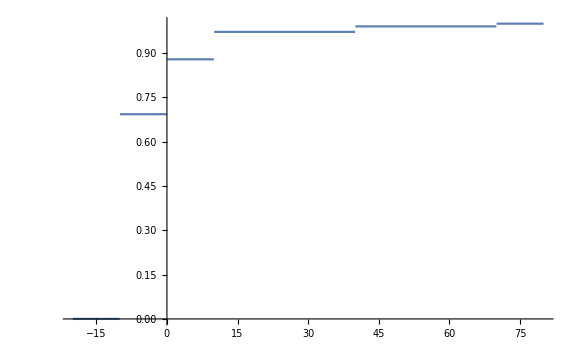

```mathematica
Show[%14,ImageSize->Large]
```